```mathematica
allData = Import["C:/Users/Evan/GitProjects/runestone/data_analysis/_sources/Final/basketball.csv"];
cumulative = Table[
{allData[[i,1]],
allData[[i,2]],
allData[[i,2]]+allData[[i,3]],
allData[[i,2]]+allData[[i,3]]+allData[[i,4]],
allData[[i,2]]+allData[[i,3]]+allData[[i,4]]+allData[[i,5]],
allData[[i,6]],
allData[[i,7]],
allData[[i,7]]+allData[[i,8]],
allData[[i,7]]+allData[[i,8]]+allData[[i,9]],
allData[[i,7]]+allData[[i,8]]+allData[[i,9]]+allData[[i,10]]},
{i,2,Length[allData]}];
diffs = Table[{
cumulative[[i,1]],cumulative[[i,6]],
cumulative[[i,2]]-cumulative[[i,7]],
cumulative[[i,3]]-cumulative[[i,8]],
cumulative[[i,4]]-cumulative[[i,9]],
cumulative[[i,5]]-cumulative[[i,10]]},
{i,1,Length[cumulative]}];
diffNoTeam = Table[
{{0,0},
{1,diffs[[i,3]]},
{2,diffs[[i,4]]},
{3,diffs[[i,5]]},
{4,diffs[[i,6]]}},
{i,1,Length[diffs]}];
```

```mathematica
meanData = Table[{i-1,Mean[diffNoTeam[[All,i,2]]]},{i,1,5}]
stdData = Table[{i-1,StandardDeviation[diffNoTeam[[All,i,2]]]},{i,1,5}]
meanFn[t_] := meanData[[5,2]] * t / 4
stdFn[t_]:=stdData[[5,2]]*Sqrt[t/4]
N[meanData[[All,2]]]
N[stdData[[All,2]]]
N[Table[meanFn[t],{t,0,4}]]
N[Table[stdFn[t],{t,0,4}]]
```

{{0,0},{1,761/1125},{2,61/45},{3,136/75},{4,2411/1125}}

{{0,0},{1,(√(18469751/1405))/15},{2,(√(533897/562))/3},{3,√(236166/1405)},{4,(√(126440977/2810))/15}}

{0.,0.676444,1.35556,1.81333,2.14311}

{0.,7.64366,10.274,12.9649,14.1416}

{0.,0.535778,1.07156,1.60733,2.14311}

{0.,7.07082,9.99964,12.247,14.1416}

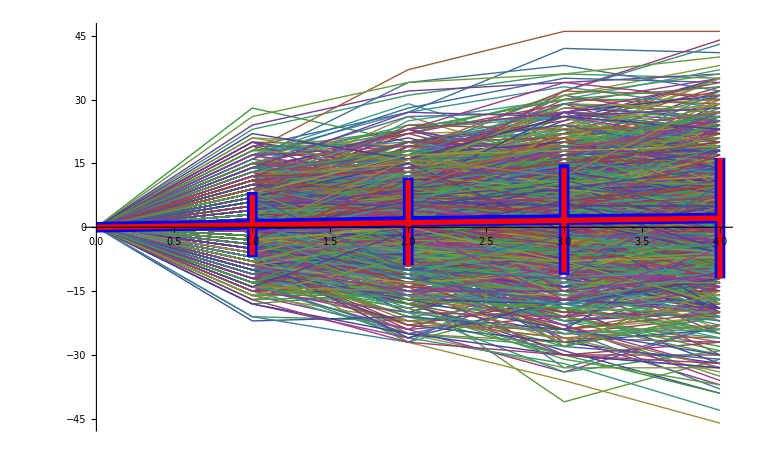

```mathematica
Needs["ErrorBarPlots`"];Show[ListLinePlot[diffNoTeam,InterpolationOrder->1],
ErrorListPlot[Table[{{t-1,meanData[[t,2]]},ErrorBar[stdData[[t,2]]]},{t,1,5}],Joined->True,PlotStyle->Directive[Thickness[0.01],Blue]],
ErrorListPlot[Table[{{t,meanFn[t]},ErrorBar[stdFn[t]]},{t,0,4}],Joined->True,PlotStyle->Directive[Thickness[0.005],Red]]]
```

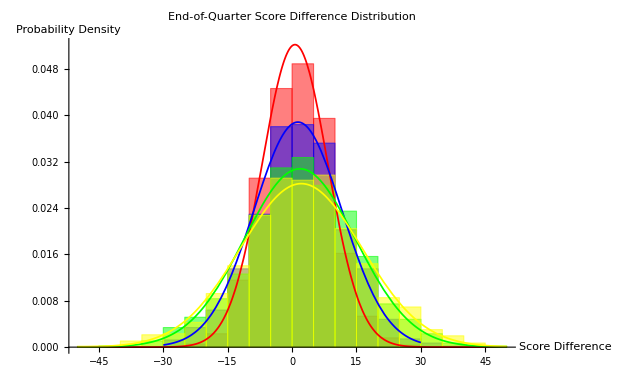

```mathematica
quarterScores=Table[diffNoTeam[[All,All,2]][[All,i]],{i,2,5}];
Show[
Histogram[quarterScores,Automatic,"PDF",ChartStyle->{Red,Blue,Green,Yellow}],
Plot[PDF[NormalDistribution[meanData[[2,2]], stdData[[2,2]]]][x],{x,-50,50},PlotStyle->Directive[Thickness[0.002],Red]],
Plot[
PDF[NormalDistribution[meanData[[3,2]], stdData[[3,2]]]][x],{x,-30,30},PlotStyle->Directive[Thickness[0.002],Blue]
],
Plot[PDF[NormalDistribution[meanData[[4,2]], stdData[[4,2]]]][x],{x,-50,50},PlotStyle->Directive[Thickness[0.002],Green]],Plot[PDF[NormalDistribution[meanData[[5,2]], stdData[[5,2]]]][x],{x,-50,50},PlotStyle->Directive[Thickness[0.002],Yellow]],
AxesStyle->Directive[FontSize->14,Bold],
AxesLabel->{"Score\nDifference", "Probability\nDensity"},
PlotLabel->Style["End-of-Quarter\nScore Difference Distribution",Large, Bold]
]
```

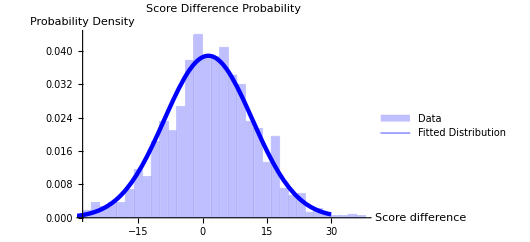
```mathematica
Export["C:/Users/Evan/GitProjects/runestone/data_analysis/_sources/Final/normalfit.png",-Graphics-,
ImageResolution->400]
```

C:/Users/Evan/GitProjects/runestone/data_analysis/_sources/Final/normalfit.png

```mathematica
Table[DistributionFitTest[quarterScores[[i]],NormalDistribution[meanData[[i+1,2]],stdData[[i+1,2]]]],{i,1,4}]
```

{0.298021,0.367163,0.506663,0.238405}

```mathematica
LinearModelFit[meanData, ptsPerQuarter,ptsPerQuarter,IncludeConstantBasis->False,ConfidenceLevel->0.99]["ParameterConfidenceIntervals"]
NonlinearModelFit[stdData,stdPerQuarter * Sqrt[t],{stdPerQuarter},{t}]["ParameterTable"]
```

{{0.458034,0.701966}}

| Estimate | Standard Error | t-Statistic | P-Value
stdPerQuarter | 7.29125 | 0.104035 | 70.0844 | 2.48357×10^-7

```mathematica
Export["C:/Users/Evan/Dropbox/Grad_School/GRFP/basketball.png",-Graphics-,ImageSize->1000]
```

C:/Users/Evan/Dropbox/Grad_School/GRFP/basketball.png

```mathematica
{{}, {}, {}, {}, {}}
```